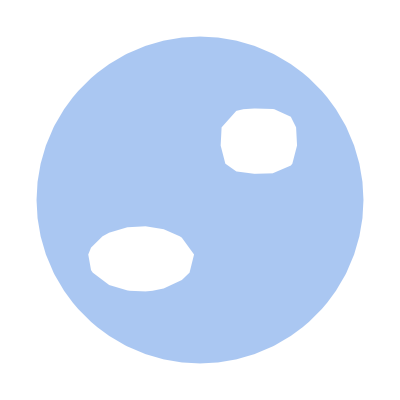

{DirichletCondition[u[x,y]==-6,0.5 Abs[-1.8+x]^3+0.8 Abs[-1.8+y]^3==0.8],DirichletCondition[u[x,y]==6,0.3 Abs[1.8+x]^2+0.8 Abs[1.8+y]^2==0.8],DirichletCondition[u[x,y]==0,x^2+y^2==25]}

{{u→InterpolatingFunction[…]}}

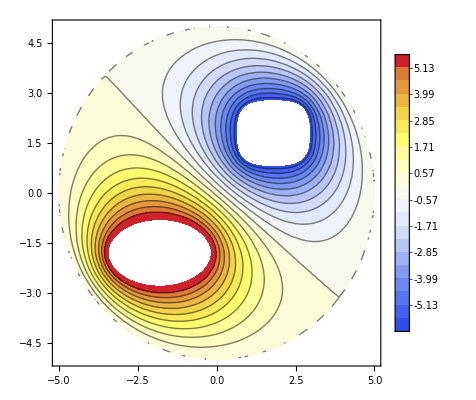

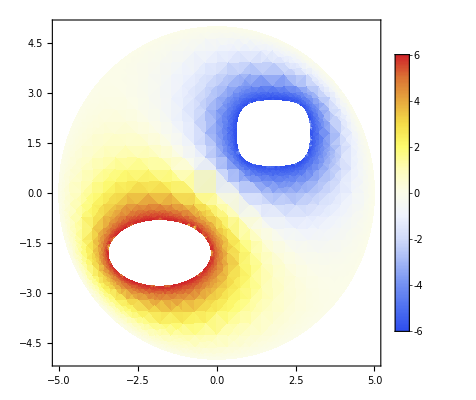

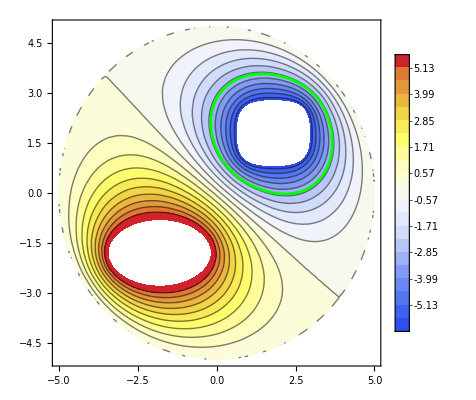

11.7873

```mathematica
outerElectrode=x^2+y^2<=25; 
electrode1=0.5*Abs[-1.8+x]^3+0.8*Abs[-1.8+y]^3<=0.8; 
electrode2=0.3*Abs[1.8+x]^2+0.8*Abs[1.8+y]^2<=0.8; 

outerRegion=ImplicitRegion[outerElectrode,{x,y}];
innerRegion1=ImplicitRegion[electrode1,{x,y}];
innerRegion2=ImplicitRegion[electrode2,{x,y}];
fullRegion=RegionDifference[RegionDifference[outerRegion,innerRegion1],innerRegion2];
Region[fullRegion]

laplEquation=Laplacian[u[x,y],{x,y}]==0;
conditions={DirichletCondition[u[x,y]==-6,0.5*Abs[-1.8+x]^3+0.8*Abs[-1.8+y]^3==0.8],
			(*^^^ Условие 1 электрода*)
		       DirichletCondition[u[x,y]==6,0.3*Abs[1.8+x]^2+0.8*Abs[1.8+y]^2==0.8],
			(*^^^ Условие 2 электрода*)
                         DirichletCondition[u[x,y]==0,x^2+y^2==25]}
			     (*^^^ Условие внешнего электрода*)	

eqSol=NDSolve[{laplEquation,conditions},u,{x,y}∈fullRegion]
eqSolPlot=ContourPlot[u[x,y]/. First[eqSol],{x,y}∈fullRegion,Contours->20,ColorFunction->"TemperatureMap",PlotLegends->Automatic]
DensityPlot[u[x,y]/. First[eqSol],{x,y}∈fullRegion,ColorFunction->"TemperatureMap",PlotLegends->Automatic]
contourPlot=ContourPlot[Evaluate[u[x,y]/. eqSol]==-3,{x,y}∈fullRegion,PlotLegends->Automatic, ContourStyle->Green];
Show[eqSolPlot,contourPlot]
points=Cases[Normal@contourPlot,Line[pts_]:>pts,Infinity];
pointPairs=Flatten[points,1];
totalDistance=0;
For[i=1,i<=Length[pointPairs]-1,i++,totalDistance+=EuclideanDistance[pointPairs[[i]],pointPairs[[i+1]]]]
totalDistance
```